## Initialization and parameters

#### Import packages and define directories

these are custom packages that should be present in ~.Mathematica/Applications/

```mathematica
<<(NotebookDirectory[]<>"NewFrame.m");
```

```mathematica
<<(NotebookDirectory[]<>"savedgxint.m");
```

ReplaceAll::reps: {y} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of bcce0bestfit12[250] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
DROOT=NotebookDirectory[]
```

/Users/tc/Dropbox/superionic-water-ice/nnp-simulation-results/nnp-p-r3-1/

```mathematica
Needs["ErrorBarPlots`"]
```

#### Define plot style options

size of graphics for output (journal column size)

```mathematica
onecol=3.4*72
twocol=6.7*72
mycol=4.5*72
```

244.8

482.4

324.

style for text

```mathematica
tstyle={FontFamily->"Helvetica",FontSize->10,SingleLetterItalics->False};
txtFormat[text_,style_:tstyle]:=Style[text,style]
```

style for drawing frames

```mathematica
framestyle=Sequence[LabelOffset->-3,PlotRangeOffset->2,FrameStyle->Directive[AbsoluteThickness[0.5],Black],LabelStyle->tstyle];
```

style for lines in plots

```mathematica
linestyles[xopts_:{}]:={
Directive[Flatten[{RGBColor[0.8,0,0],AbsoluteThickness[1],xopts}]],
Directive[Flatten[{RGBColor[0.1,0.2,0.9],AbsoluteThickness[1],xopts}]],
Directive[Flatten[{RGBColor[0.0,0.5,0.1],AbsoluteThickness[1],xopts}]],
Directive[Flatten[{RGBColor[0.5,0.5,0.5],AbsoluteThickness[1],xopts}]],
Directive[Flatten[{Black,AbsoluteThickness[1],xopts}]]
}
linedashing=Directive[AbsoluteDashing[{2,4,2,4,2,4}]];
fillstyles[xopts_:{},mix_:0.75]:={
Directive[Flatten[{Blend[{RGBColor[0.8,0,0],White},mix],xopts}]],
Directive[Flatten[{Blend[{RGBColor[0.1,0.2,0.9],White},mix],xopts}]],
Directive[Flatten[{Blend[{RGBColor[0.0,0.5,0.1],White},mix],xopts}]],
Directive[Flatten[{Blend[{RGBColor[0.5,0.5,0.5],White},mix],xopts}]]
}
```

style for color scales

```mathematica
Module[{f},
cbarHot[alpha_,range_:{0,1},opfun_:((1.0)&)]:=Directive[f=Min[1,Max[0,(alpha-range[[1]])/(range[[2]]-range[[1]])]];
Blend[{
Blend[{ColorData["DeepSeaColors"][(1-f)^1.1],White},(1-f)^4],
RGBColor[1.0,0.5,0]},(f)^10
]
,Opacity[opfun[(alpha-range[[1]])/(range[[2]]-range[[1]])]]
]
];
```

```mathematica
Module[{f},
cbarBWR[alpha_,range_:{0,1},opfun_:((1.0)&)]:=Directive[f=Min[1,Max[0,(alpha-range[[1]])/(range[[2]]-range[[1]])]];
Blend[{RGBColor[1,0.3,0],RGBColor[0,0.4,1],White,Black},{Sin[f*Pi/2],Cos[f*Pi/2],Sin[f*Pi]^4*2+Sin[f*Pi]^16*4+Sin[f*Pi]^64*8+Sin[f*Pi]^256*32,Cos[f*Pi]^16}] ,Opacity[opfun[(alpha-range[[1]])/(range[[2]]-range[[1]])]]
]
];
```

plot markers

```mathematica
plotmark[style_: linestyles[][[1]],stylein_: Directive[White],sz_: 1.5]:=Graphics[{style,EdgeForm[style],FaceForm[stylein],#}]&/@{Disk[{0,0},Offset[{sz,sz}]],Polygon[{Offset[{0,sz}*Sqrt[Pi/2]],Offset[{sz,0}*Sqrt[Pi/2]],Offset[{0,-sz}*Sqrt[Pi/2]],Offset[{-sz,0}*Sqrt[Pi/2]]}],Polygon[{Offset[{sz,sz}*Sqrt[Pi/4]],Offset[{sz,-sz}*Sqrt[Pi/4]],Offset[{-sz,-sz}*Sqrt[Pi/4]],Offset[{-sz,sz}*Sqrt[Pi/4]]}],Polygon[{Offset[{-sz,-sz*Sqrt[3]/2}],Offset[{sz,-sz*Sqrt[3]/2}],Offset[{0,sz*Sqrt[3]}]}],Polygon[{Offset[{-sz,sz*Sqrt[3]/2}],Offset[{sz,sz*Sqrt[3]/2}],Offset[{0,-sz*Sqrt[3]}]}],{Line[{Offset[{sz,sz}],Offset[-{sz,sz}]}],Line[{Offset[{sz,-sz}],Offset[{-sz,sz}]}]}}
```

```mathematica
bigplotmark[style_: linestyles[][[1]],stylein_: Directive[White],sz_: 3]:=Graphics[{style,EdgeForm[style],FaceForm[stylein],#}]&/@{Disk[{0,0},Offset[{sz,sz}]],Polygon[{Offset[{0,sz}*Sqrt[Pi/2]],Offset[{sz,0}*Sqrt[Pi/2]],Offset[{0,-sz}*Sqrt[Pi/2]],Offset[{-sz,0}*Sqrt[Pi/2]]}],Polygon[{Offset[{sz,sz}*Sqrt[Pi/4]],Offset[{sz,-sz}*Sqrt[Pi/4]],Offset[{-sz,-sz}*Sqrt[Pi/4]],Offset[{-sz,sz}*Sqrt[Pi/4]]}],Polygon[{Offset[{-sz,-sz*Sqrt[3]/2}],Offset[{sz,-sz*Sqrt[3]/2}],Offset[{0,sz*Sqrt[3]}]}],Polygon[{Offset[{-sz,sz*Sqrt[3]/2}],Offset[{sz,sz*Sqrt[3]/2}],Offset[{0,-sz*Sqrt[3]}]}],{Line[{Offset[{sz,sz}],Offset[-{sz,sz}]}],Line[{Offset[{sz,-sz}],Offset[{-sz,sz}]}]}}
```

```mathematica
cbarRED[a_]:=RGBColor[a,0.0,0.0]
```

```mathematica
cbarBLUE[a_]:=RGBColor[a,0,1-a]
```

```mathematica
Table[RGBColor[i,0.0,0.0],{i,0,1,0.02}]
```

{RGBColor[0., 0., 0.],RGBColor[0.02, 0., 0.],RGBColor[0.04, 0., 0.],RGBColor[0.06, 0., 0.],RGBColor[0.08, 0., 0.],RGBColor[0.1, 0., 0.],RGBColor[0.12, 0., 0.],RGBColor[0.14, 0., 0.],RGBColor[0.16, 0., 0.],RGBColor[0.18, 0., 0.],RGBColor[0.2, 0., 0.],RGBColor[0.22, 0., 0.],RGBColor[0.24, 0., 0.],RGBColor[0.26, 0., 0.],RGBColor[0.28, 0., 0.],RGBColor[0.3, 0., 0.],RGBColor[0.32, 0., 0.],RGBColor[0.34, 0., 0.],RGBColor[0.36, 0., 0.],RGBColor[0.38, 0., 0.],RGBColor[0.4, 0., 0.],RGBColor[0.42, 0., 0.],RGBColor[0.44, 0., 0.],RGBColor[0.46, 0., 0.],RGBColor[0.48, 0., 0.],RGBColor[0.5, 0., 0.],RGBColor[0.52, 0., 0.],RGBColor[0.54, 0., 0.],RGBColor[0.56, 0., 0.],RGBColor[0.58, 0., 0.],RGBColor[0.6, 0., 0.],RGBColor[0.62, 0., 0.],RGBColor[0.64, 0., 0.],RGBColor[0.66, 0., 0.],RGBColor[0.68, 0., 0.],RGBColor[0.7000000000000001, 0., 0.],RGBColor[0.72, 0., 0.],RGBColor[0.74, 0., 0.],RGBColor[0.76, 0., 0.],RGBColor[0.78, 0., 0.],RGBColor[0.8, 0., 0.],RGBColor[0.8200000000000001, 0., 0.],RGBColor[0.84, 0., 0.],RGBColor[0.86, 0., 0.],RGBColor[0.88, 0., 0.],RGBColor[0.9, 0., 0.],RGBColor[0.92, 0., 0.],RGBColor[0.9400000000000001, 0., 0.],RGBColor[0.96, 0., 0.],RGBColor[0.98, 0., 0.],RGBColor[1., 0., 0.]}

```mathematica
Table[RGBColor[i,i*0.0,1-i],{i,0,1,0.02}]
```

{RGBColor[0., 0., 1.],RGBColor[0.02, 0., 0.98],RGBColor[0.04, 0., 0.96],RGBColor[0.06, 0., 0.94],RGBColor[0.08, 0., 0.92],RGBColor[0.1, 0., 0.9],RGBColor[0.12, 0., 0.88],RGBColor[0.14, 0., 0.86],RGBColor[0.16, 0., 0.84],RGBColor[0.18, 0., 0.8200000000000001],RGBColor[0.2, 0., 0.8],RGBColor[0.22, 0., 0.78],RGBColor[0.24, 0., 0.76],RGBColor[0.26, 0., 0.74],RGBColor[0.28, 0., 0.72],RGBColor[0.3, 0., 0.7],RGBColor[0.32, 0., 0.6799999999999999],RGBColor[0.34, 0., 0.6599999999999999],RGBColor[0.36, 0., 0.64],RGBColor[0.38, 0., 0.62],RGBColor[0.4, 0., 0.6],RGBColor[0.42, 0., 0.5800000000000001],RGBColor[0.44, 0., 0.56],RGBColor[0.46, 0., 0.54],RGBColor[0.48, 0., 0.52],RGBColor[0.5, 0., 0.5],RGBColor[0.52, 0., 0.48],RGBColor[0.54, 0., 0.45999999999999996],RGBColor[0.56, 0., 0.43999999999999995],RGBColor[0.58, 0., 0.42000000000000004],RGBColor[0.6, 0., 0.4],RGBColor[0.62, 0., 0.38],RGBColor[0.64, 0., 0.36],RGBColor[0.66, 0., 0.33999999999999997],RGBColor[0.68, 0., 0.31999999999999995],RGBColor[0.7000000000000001, 0., 0.29999999999999993],RGBColor[0.72, 0., 0.28],RGBColor[0.74, 0., 0.26],RGBColor[0.76, 0., 0.24],RGBColor[0.78, 0., 0.21999999999999997],RGBColor[0.8, 0., 0.19999999999999996],RGBColor[0.8200000000000001, 0., 0.17999999999999994],RGBColor[0.84, 0., 0.16000000000000003],RGBColor[0.86, 0., 0.14],RGBColor[0.88, 0., 0.12],RGBColor[0.9, 0., 0.09999999999999998],RGBColor[0.92, 0., 0.07999999999999996],RGBColor[0.9400000000000001, 0., 0.05999999999999994],RGBColor[0.96, 0., 0.040000000000000036],RGBColor[0.98, 0., 0.020000000000000018],RGBColor[1., 0., 0.]}

## Cation interstitials model

### initialization/definition

```mathematica
empiricalD[{D0_,gamma_,T0_},x_]:=D0*(x/T0-1.)^gamma
```

```mathematica
G[{e0_,lambda_,g_,kbT_},x_]:= x(e0-(1/2)lambda*x)+kbT( x Log[x]+(1-x)Log[1-x]-x*Log[g])
```

```mathematica
Manipulate[
Show[{
Plot[{
G[{e0,lambda,g,kbT},x]},{x,0,1},PlotRange->{{-0.01,1.01},All},Frame->True,Axes->False,FrameLabel->{"x","G"},FrameStyle->Directive[Black,Dashing[{}]],PlotStyle->{Directive[Thin,Dashed,Red],Directive[{Thick,RGBColor[0.5,0,0]}]} ]
}],
{{e0,1.0,"e0"},0,10,Appearance->"Labeled"},
{{lambda,2.5,"lambda"},0,5,Appearance->"Labeled"},
{{kbT,1,"kbT"},0,10,Appearance->"Labeled"},
{{g,1,"g"},1,8,Appearance->"Labeled"},
SaveDefinitions->True
]
```

```mathematica
Simplify[D[G[{e0,lambda,g,kbT},x],x]]
```

e0-lambda x-kbT (Log[g]+Log[1-x]-Log[x])

```mathematica
Simplify[D[D[G[{e0,lambda,g,kbT},x],x],x]]
```

-lambda+kbT/(x-x^2)

```mathematica
dG[{e0_,lambda_,g_,kbT_},x_]:=e0-lambda x-kbT (Log[g]+Log[1-x]-Log[x])
```

```mathematica
ddG[{lambda_,kbT_},x_]:=-lambda+kbT/(x-x^2)
```

```mathematica
G[{1,1,1,0.1},0.001]
```

0.000208774

```mathematica
G[{1,1,1,0.1},1-0.001]
```

0.499209

```mathematica
Table[{t,FindMinimum[{G[{1,1,1,t},x],0<x<1},x]},{t,0.01,1,0.05}]
```

{{0.01,{8.15386×10^-8,{x→9.83984×10^-8}}},{0.06,{5.19245×10^-8,{x→6.2592×10^-7}}},{0.11,{-0.0000124007,{x→0.000113612}}},{0.16,{-0.000310454,{x→0.00195089}}},{0.21,{-0.00182517,{x→0.00883843}}},{0.26,{-0.00573356,{x→0.0227874}}},{0.31,{-0.0129091,{x→0.0437431}}},{0.36,{-0.0237602,{x→0.0702675}}},{0.41,{-0.0382841,{x→0.100243}}},{0.46,{-0.0561911,{x→0.131457}}},{0.51,{-0.0770375,{x→0.162053}}},{0.56,{-0.100336,{x→0.190762}}},{0.61,{-0.125626,{x→0.216913}}},{0.66,{-0.152513,{x→0.240294}}},{0.71,{-0.180672,{x→0.260982}}},{0.76,{-0.209845,{x→0.279203}}},{0.81,{-0.239833,{x→0.295239}}},{0.86,{-0.270477,{x→0.309372}}},{0.91,{-0.301657,{x→0.321868}}},{0.96,{-0.333276,{x→0.332958}}}}

```mathematica
lambdacritical[e0_,g_]:=e0*(2/(1+Log[g]/2))
```

```mathematica
lambdacritical[1,8]
```

2/(1+Log[8]/2)

```mathematica
tc[e0_,lambda_,g_]:=(e0-lambda/2)/Log[g]
```

```mathematica
gnow=12;e0now=1;
```

NMinimize::nnum: The function value Indeterminate is not a number at {x} = {0.}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

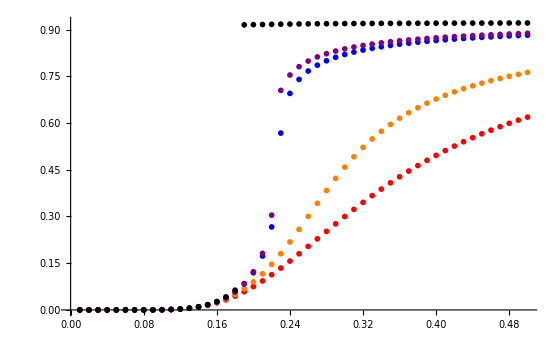

```mathematica
ListPlot[{
Table[{t,x/.NMinimize[{G[{1,0,gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}],
Table[{t,x/.NMinimize[{G[{1,0.5*lambdacritical[1,gnow],gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}],
Table[{t,x/.NMinimize[{G[{1,0.97*lambdacritical[1,gnow],gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}],
Table[{t,x/.NMinimize[{G[{1,1.0*lambdacritical[1,gnow],gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}],
Table[{t,x/.NMinimize[{G[{1,1.2*lambdacritical[1,gnow],gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}]
},Joined->False, PlotStyle->{Red,Orange,Blue,Purple,Black}, PlotRange->{All,All}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {x} = {0.}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

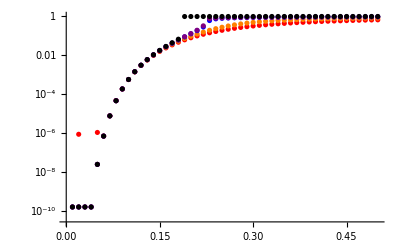

```mathematica
ListLogPlot[{
Table[{t,x/.NMinimize[{G[{1,0,gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}],
Table[{t,x/.NMinimize[{G[{1,0.5*lambdacritical[1,gnow],gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}],
Table[{t,x/.NMinimize[{G[{1,0.97*lambdacritical[1,gnow],gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}],
Table[{t,x/.NMinimize[{G[{1,1.0*lambdacritical[1,gnow],gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}],
Table[{t,x/.NMinimize[{G[{1,1.2*lambdacritical[1,gnow],gnow,t},x],0<x<1},x][[2]]},{t,0.01,0.5,0.01}]
},Joined->False, PlotStyle->{Red,Orange,Blue,Purple,Black}, PlotRange->{All,All}]
```

## Read data

```mathematica
DDIR=DROOT<>"npt/";
```

```mathematica
systemlist={"fcc","bcc","Pbcm"}
```

{fcc,bcc,Pbcm}

```mathematica
pressurelist = {20, 30,50,75,100,125,150,175,200,250,300, 350, 400,450, 500,550, 600,700, 800};
```

fcc is stable at P>=250 GPa

```mathematica
highP=Cases[pressurelist,p_/;700>=p≥100];
```

pbcm is stable at P>=400 GPa

```mathematica
hhighP=Cases[pressurelist,p_/;700>=p≥100];
```

bcc is stable at P <= 250 GPa

```mathematica
lowP=Cases[pressurelist,p_/;p<=250];
```

This is the conversion from Kb*K to eV

```mathematica
kbK2ev=0.00008661733;
```

diffusivity units in cm^2/s

```mathematica
Clear[ddata]
```

format : P[GPa]  T[K]  D_O    D_O_error  D_H  D_H_error

```mathematica
Do[ddata[s,p]=Cases[If[FileExistsQ[DDIR<>"D-"<>s<>".dat"],Import[DDIR<>"D-"<>s<>".dat","Table"]],
{pp_,tt_,do_,_,dh_,_}/;pp==p &&NumericQ[do]]
,{s,{"fcc","Pbcm"}},{p,highP}]
```

```mathematica
Do[ddata[s,p]=Cases[If[FileExistsQ[DDIR<>"D-"<>s<>".dat"],Import[DDIR<>"D-"<>s<>".dat","Table"]],
{pp_,tt_,do_,_,dh_,_}/;pp==p &&NumericQ[do]]
,{s,{"bcc"}},{p,lowP}]
```

## Preprocessing the D data

plot Log(D) on the y axis, and 1000/T on the x-axis. then from the expression log[D] = C1+C2*(1000/T)

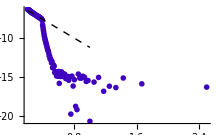

```mathematica
Show[{
Table[
ListPlot[
{1000./#1[[2]],Log[#1[[5]]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 ]
,Joined->False,PlotMarkers->plotmark[cbarBLUE[p/400.],White][[1]],PlotStyle->Directive[AbsoluteThickness[1],cbarBLUE[p/800.]]]
,{p,{200}}],
Table[
ListPlot[
{1000./#1[[2]],Log[#1[[5]]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;do>1*^-4 ]
,Joined->False,PlotMarkers->plotmark[cbarBLUE[p/400.],White][[1]],PlotStyle->Directive[Dashed,AbsoluteThickness[1],cbarBLUE[p/800.]]]
,{p,{200}}],
Plot[
-5.3-5.9*x,{x,1000/5000,1.},PlotRange->{All,All},
Frame->True,Axes->True,FrameLabel->{"T","D"},
FrameStyle->Directive[Black,Dashing[{}]],PlotStyle->Directive[Thick,Dashed,Black] ]
},
PlotRange->{All, All}]
```

General::munfl: Exp[-57767.5] is too small to represent as a normalized machine number; precision may be lost.

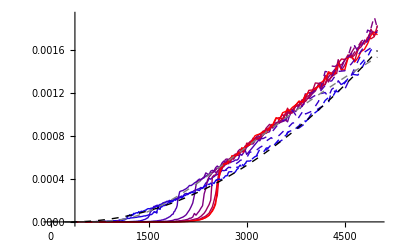

```mathematica
Show[{
Table[
ListPlot[
{#1[[2]],#1[[5]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4]
,Joined->True,PlotStyle->Directive[AbsoluteThickness[1],cbarBLUE[p/250.]]]
,{p,pressurelist}],
Table[
ListPlot[
{#1[[2]],#1[[5]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;do>1*^-4]
,Joined->True,PlotStyle->Directive[Dashed,AbsoluteThickness[1],cbarBLUE[p/250.]]]
,{p,pressurelist}],
Plot[
empiricalD[{6.5*^-6,2.,300},x],{x,0,5000},PlotRange->{All,All},
Frame->True,Axes->False,FrameLabel->{"T","D"},
FrameStyle->Directive[Black,Dashing[{}]],PlotStyle->Directive[Thick,Dashed,Black] ],
Plot[
Exp[-5.3-5.9*(1000/x)],{x,0,5000},PlotRange->{All,All},
Frame->True,Axes->False,FrameLabel->{"T","D"},
FrameStyle->Directive[Black,Dashing[{}]],PlotStyle->Directive[Thick,Dashed,Gray] ]
},
PlotRange->{All,All}]
```

```mathematica
{pp_,tt_,do_,_,dh_,_}/;do<1*^-4
```

{pp_,tt_,do_,_,dh_,_}/;do<1/10000

```mathematica
Remove[fitest]
```

```mathematica
Do[
errors=#1[[6]]&/@Cases[ddata["fcc",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&dh>0.0007];
fitest["fcc"][p]=NonlinearModelFit[
{#1[[2]],#1[[5]]}&/@Cases[ddata["fcc",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&dh>0.0007],
empiricalD[{estD0,estgamma,1000},x],
{{estD0,0.},{estgamma,1},{estT0,1000}},
x,Weights->1/errors^2,MaxIterations->10000],{p,highP}]
```

```mathematica
Do[
errors=#1[[6]]&/@Cases[ddata["Pbcm",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&dh>0.0007];
fitest["Pbcm"][p]=NonlinearModelFit[
{#1[[2]],#1[[5]]}&/@Cases[ddata["Pbcm",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&dh>0.0007],
empiricalD[{estD0,estgamma,1000},x],
{{estD0,0.},{estgamma,1},{estT0,1000}},
x,Weights->1/errors^2,MaxIterations->10000],{p,highP}]
```

```mathematica
Do[fitest["bcc"][p]=NonlinearModelFit[
{#1[[2]],#1[[5]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;dh>0.0007],
empiricalD[{estD0,estgamma,600},x],{{estD0,0.0004},{estgamma,2},{estT0,600}},x,MaxIterations->10000],{p,lowP}]
```

```mathematica
Table[{p,fitest["fcc"][p]["BestFitParameters"]},{p,highP}]
```

{{100,{estD0→0.000334829,estgamma→1.1145,estT0→1000.}},{125,{estD0→0.000356222,estgamma→1.12417,estT0→1000.}},{150,{estD0→0.000327225,estgamma→1.20893,estT0→1000.}},{175,{estD0→0.000326337,estgamma→1.19969,estT0→1000.}},{200,{estD0→0.000316417,estgamma→1.2374,estT0→1000.}},{250,{estD0→0.000312893,estgamma→1.24,estT0→1000.}},{300,{estD0→0.000304204,estgamma→1.24659,estT0→1000.}},{350,{estD0→0.000283312,estgamma→1.29533,estT0→1000.}},{400,{estD0→0.000283476,estgamma→1.2781,estT0→1000.}},{450,{estD0→0.000289292,estgamma→1.23813,estT0→1000.}},{500,{estD0→0.000302339,estgamma→1.18952,estT0→1000.}},{550,{estD0→0.000295444,estgamma→1.19502,estT0→1000.}},{600,{estD0→0.000310867,estgamma→1.13907,estT0→1000.}},{700,{estD0→0.000306038,estgamma→1.1226,estT0→1000.}}}

```mathematica
Table[{p,fitest["Pbcm"][p]["BestFitParameters"]},{p,highP}]
```

{{100,{estD0→0.000365014,estgamma→1.03504,estT0→1000.}},{125,{estD0→0.000370962,estgamma→1.07806,estT0→1000.}},{150,{estD0→0.000317695,estgamma→1.23348,estT0→1000.}},{175,{estD0→0.000320618,estgamma→1.25148,estT0→1000.}},{200,{estD0→0.000302705,estgamma→1.29267,estT0→1000.}},{250,{estD0→0.000295743,estgamma→1.29698,estT0→1000.}},{300,{estD0→0.000279646,estgamma→1.34974,estT0→1000.}},{350,{estD0→0.000306454,estgamma→1.23105,estT0→1000.}},{400,{estD0→0.000278492,estgamma→1.29981,estT0→1000.}},{450,{estD0→0.000274423,estgamma→1.30577,estT0→1000.}},{500,{estD0→0.000298042,estgamma→1.19488,estT0→1000.}},{550,{estD0→0.000312129,estgamma→1.13696,estT0→1000.}},{600,{estD0→0.00029,estgamma→1.18119,estT0→1000.}},{700,{estD0→0.000301547,estgamma→1.1126,estT0→1000.}}}

```mathematica
Table[{p,fitest["bcc"][p]["BestFitParameters"]},{p,lowP}]
```

{{20,{estD0→0.0000398923,estgamma→1.86213,estT0→600.}},{30,{estD0→0.0000405107,estgamma→1.84943,estT0→600.}},{50,{estD0→0.0000575277,estgamma→1.68654,estT0→600.}},{75,{estD0→0.0000714491,estgamma→1.60679,estT0→600.}},{100,{estD0→0.000070377,estgamma→1.63664,estT0→600.}},{125,{estD0→0.0000737305,estgamma→1.61395,estT0→600.}},{150,{estD0→0.0000844207,estgamma→1.53562,estT0→600.}},{175,{estD0→0.0000829073,estgamma→1.54249,estT0→600.}},{200,{estD0→0.0000878634,estgamma→1.51299,estT0→600.}},{250,{estD0→0.000100239,estgamma→1.43643,estT0→600.}}}

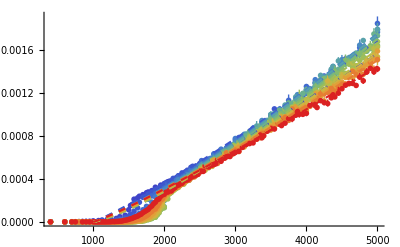

```mathematica
Dfcc=Show[{
Table[
ErrorListPlot[{{#1[[2]],#1[[5]]},ErrorBar[#1[[6]]]}&/@Cases[ddata["fcc",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4]
,Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[Dashed,AbsoluteThickness[1],ColorData["Rainbow"][p/700.]]]
,{p,highP}],
Table[
Plot[
fitest["fcc"][p][x],{x,0,5000},PlotRange->{All,All},
PlotStyle->Directive[Dashed,AbsoluteThickness[1.5],ColorData["Rainbow"][p/700.]] ]
,{p,highP}]
},
PlotRange->{All,All}]
```

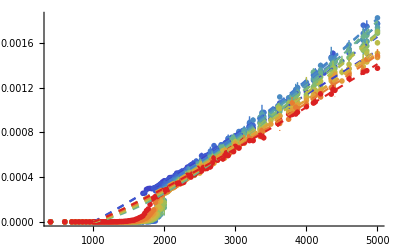

```mathematica
DPbcm=Show[{
Table[
ErrorListPlot[{{#1[[2]],#1[[5]]},ErrorBar[#1[[6]]]}&/@Cases[ddata["Pbcm",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4]
,Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[Dashed,AbsoluteThickness[1],ColorData["Rainbow"][p/700.]]]
,{p,highP}],
Table[
Plot[
fitest["Pbcm"][p][x],{x,0,5000},PlotRange->{All,All},
PlotStyle->Directive[Dashed,AbsoluteThickness[1.5],ColorData["Rainbow"][p/700.]] ]
,{p,highP}]
},
PlotRange->{All,All}]
```

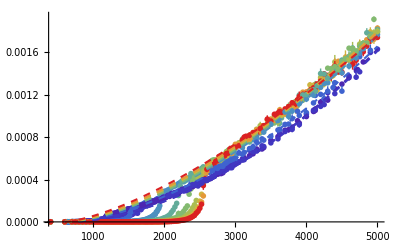

```mathematica
Dbcc=Show[{
Table[
ErrorListPlot[{{#1[[2]],#1[[5]]},ErrorBar[#1[[6]]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4],
Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/250.],ColorData["Rainbow"][p/250.]][[2]],
PlotStyle->Directive[AbsoluteThickness[1],ColorData["Rainbow"][p/250.]]]
,{p,lowP}],
Table[
ErrorListPlot[{{#1[[2]],#1[[5]]},ErrorBar[#1[[6]]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;do>1*^-4]
,Joined->False,PlotMarkers->plotmark[ColorData["DarkRainbow"][p/250.],White][[2]],
PlotStyle->Directive[Dashed,AbsoluteThickness[1],ColorData["Rainbow"][p/250.]]]
,{p,lowP}],
Table[
Plot[
fitest["bcc"][p][x],{x,0,5000},PlotRange->{All,All},
PlotStyle->Directive[Dashed,AbsoluteThickness[1.5],ColorData["Rainbow"][p/250.] ]]
,{p,lowP}]
},
PlotRange->{All,All}]
```

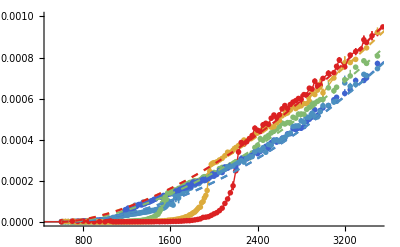

```mathematica
Dbcc=Show[{
Table[
ErrorListPlot[{{#1[[2]],#1[[5]]},ErrorBar[#1[[6]]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4],
Joined->True,PlotMarkers->plotmark[ColorData["Rainbow"][p/100.],ColorData["Rainbow"][p/100.]][[2]],
PlotStyle->Directive[AbsoluteThickness[1],ColorData["Rainbow"][p/100.]]]
,{p,{20,30,50,75,100}}],
Table[
ErrorListPlot[{{#1[[2]],#1[[5]]},ErrorBar[#1[[6]]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;do>1*^-4]
,Joined->False,PlotMarkers->plotmark[ColorData["DarkRainbow"][p/100.],White][[2]],
PlotStyle->Directive[Dashed,AbsoluteThickness[1],ColorData["Rainbow"][p/100.]]]
,{p,{20,30,50,75,100}}],
Table[
Plot[
fitest["bcc"][p][x],{x,0,5000},PlotRange->{All,All},
PlotStyle->Directive[Dashed,AbsoluteThickness[1.5],ColorData["Rainbow"][p/100.] ]]
,{p,{20,30,50,75,100}}]
},
PlotRange->{{500,3500},{0,0.001}},Axis->True]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

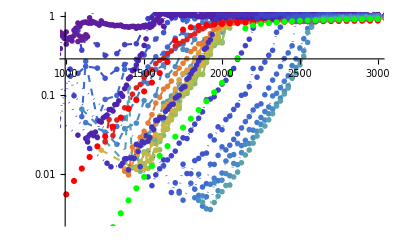

```mathematica
e0now=8000;
Show[{
Table[
ListLogPlot[{#1[[2]],#1[[5]]/fitest["fcc"][p][#1[[2]]]}&/@Cases[ddata["fcc",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6],
Joined->True,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/800.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.5],ColorData["Rainbow"][p/700.],Dashed],PlotRange->{All,All}]
,{p,highP}],
Table[
ListLogPlot[{#1[[2]],#1[[5]]/fitest["bcc"][p][#1[[2]]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6],
Joined->True,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.5],ColorData["Rainbow"][p/700.], Dotted],PlotRange->{All,All}]
,{p,lowP}],
ListLogPlot[{
Table[{t,x/.NMinimize[{G[{8000,0.98*lambdacritical[8000,16],16,t},x],0<x<1},x][[2]]},{t,1000,3000,50}],
Table[{t,x/.NMinimize[{G[{14000,lambdacritical[14000,100],100,t},x],0<x<1},x][[2]]},{t,1000,3000,50}]
},Joined->False, PlotStyle->{Red,Green}, PlotRange->{All,All}]
}, PlotRange->{{1000,3000},{-6,0}}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

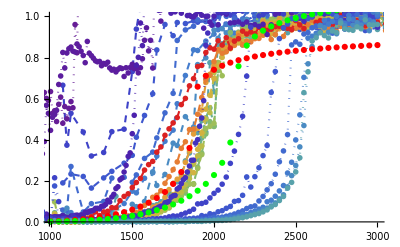

```mathematica
e0now=8000;
Show[{
Table[
ListPlot[{#1[[2]],#1[[5]]/fitest["fcc"][p][#1[[2]]]}&/@ddata["fcc",p],
Joined->True,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.5],ColorData["Rainbow"][p/700.],Dashed],PlotRange->{All,All}]
,{p,highP}],
Table[
ListPlot[{#1[[2]],#1[[5]]/fitest["bcc"][p][#1[[2]]]}&/@ddata["bcc",p],
Joined->True,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.5],ColorData["Rainbow"][p/700.], Dotted],PlotRange->{All,All}]
,{p,lowP}],
ListPlot[{
Table[{t,x/.NMinimize[{G[{8300,0.99*lambdacritical[8300,12],12,t},x],0<x<1},x][[2]]},{t,1000,3000,50}],
Table[{t,1.25*x/.NMinimize[{G[{9500,0.99*lambdacritical[9500,12],12,t},x],0<x<1},x][[2]]},{t,1000,3000,50}]
},Joined->False, PlotStyle->{Red,Green}, PlotRange->{All,All}]
}, PlotRange->{{1000,3000},{0,1}}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {x} = {0.}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

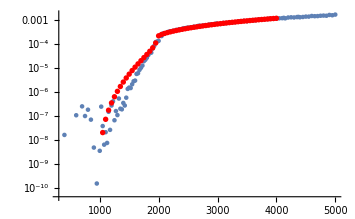

```mathematica
e0now=8771;
Show[{
ListLogPlot[{#1[[2]],#1[[5]]}&/@ddata["fcc",400],Joined->False,PlotRange->{All,All}],
ListLogPlot[{
{#1[[1]],1.16*fitest["fcc"][400][#1[[1]]]*#1[[2]]}&/@ Table[{t,x/.NMinimize[{G[{e0now,0.995*lambdacritical[e0now,12],12,t},x],0<x<1},x][[2]]},{t,100,4000,50}]
},Joined->False, PlotStyle->{Red}, PlotRange->{All,All}]
}]
```

## Do the fits properly

```mathematica
inttlist={800,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3500,4000,4500,5000};
```

```mathematica
gxint[e0_,g0_,cr_]:= gxint[e0,g0,cr]=Interpolation[Table[{t,y/.NMinimize[{G[{e0,cr*lambdacritical[e0,g0],g0,t},y],0<y<1},y][[2]]},{t,inttlist}], InterpolationOrder->3]
```

```mathematica
gxintfunc[e0_,g0_,cr_,x_]:=Evaluate[gxint[e0,g0,cr]][x]
```

```mathematica
gxint2[e0_,g0_,cr_,x_]:=Evaluate[gxint[e0,g0,cr]][x]/Evaluate[gxint[e0,g0,cr]][5000]
```

```mathematica
loss[e0fit_,g0fit_,crfit_,fitdata_]:=Total[Abs[(gxint2[e0fit,g0fit,crfit,#1[[1]]]-#1[[2]])^2.]&/@fitdata]
```

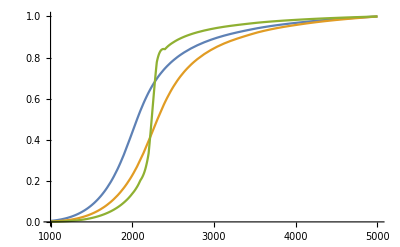

```mathematica
Plot[{gxint2[8000,12,0.75,x],gxint2[9000,12,0.75,x],gxint2[10000,12,0.995,x] },{x,1000,5000}]
```

## fits for fcc

```mathematica
fitest["fcc"][100]
```

FittedModel[0.000334829 (-1.+x/1000)^1.1145]

```mathematica
Clear[fitdatanow]
```

```mathematica
Table[
fitdatanow[pnow]={#1[[2]],Re[#1[[5]]/fitest["fcc"][pnow][#1[[2]]]]}&/@Cases[ddata["fcc",pnow],{pp_,tt_,do_,_,dh_,_}/;tt>1000 &&tt< 3000];
int=Interpolation[ Flatten[Table[{{e0,cr0},loss[e0,12,cr0,fitdatanow[pnow]]},
{e0,6500,9000,125},{cr0,0.7,1.0,0.0125}],1]];
bestfit=NMinimize[{int[x,y],0.7<y<1,6500<x<9000},{x,y}];
e0bestfit12[pnow]={x,y}/.bestfit[[2]];
errors=#1[[6]]&/@Cases[ddata["fcc",pnow],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&tt>1500];
fitest["fcc"][pnow]=NonlinearModelFit[
{#1[[2]],Re[#1[[5]]/gxint2[e0bestfit12[pnow][[1]],12,e0bestfit12[pnow][[2]],#1[[2]]]]}&/@Cases[ddata["fcc",pnow],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&tt>1500],
empiricalD[{estD0,estgamma,1000},x],
{{estD0,0.},{estgamma,1},{estT0,1000}},
x,MaxIterations->10000];
{pnow,bestfit,fitest["fcc"][pnow]["BestFitParameters"]}
,{pnow,highP},{loop,1,4}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{{100,{0.524016,{x→6553.52,y→0.991462}},{estD0→0.000376654,estgamma→1.00086,estT0→1000.}},{100,{0.523994,{x→6553.52,y→0.991461}},{estD0→0.000376654,estgamma→1.00086,estT0→1000.}},{100,{0.523992,{x→6553.52,y→0.991461}},{estD0→0.000376654,estgamma→1.00086,estT0→1000.}},{100,{0.523991,{x→6553.52,y→0.991461}},{estD0→0.000376654,estgamma→1.00086,estT0→1000.}}},{{125,{0.262267,{x→6803.86,y→0.990138}},{estD0→0.000358374,estgamma→1.11896,estT0→1000.}},{125,{0.249435,{x→6804.8,y→0.98795}},{estD0→0.000358906,estgamma→1.11767,estT0→1000.}},{125,{0.246477,{x→6805.07,y→0.987359}},{estD0→0.000359052,estgamma→1.11732,estT0→1000.}},{125,{0.245681,{x→6805.15,y→0.987193}},{estD0→0.000359093,estgamma→1.11722,estT0→1000.}}},{{150,{0.319767,{x→7611.81,y→1.}},{estD0→0.000349876,estgamma→1.16417,estT0→1000.}},{150,{0.142399,{x→7500.,y→0.975}},{estD0→0.000356165,estgamma→1.14918,estT0→1000.}},{150,{0.116575,{x→7500.,y→0.973076}},{estD0→0.000357185,estgamma→1.14665,estT0→1000.}},{150,{0.113321,{x→7500.,y→0.972689}},{estD0→0.000357384,estgamma→1.14615,estT0→1000.}}},{{175,{0.10127,{x→7675.16,y→0.985073}},{estD0→0.000342919,estgamma→1.17003,estT0→1000.}},{175,{0.0434283,{x→7672.9,y→0.957588}},{estD0→0.000353147,estgamma→1.14509,estT0→1000.}},{175,{0.0241875,{x→7598.89,y→0.9375}},{estD0→0.000357007,estgamma→1.13662,estT0→1000.}},{175,{0.0199101,{x→7603.91,y→0.934734}},{estD0→0.000358616,estgamma→1.13271,estT0→1000.}}},{{200,{0.160423,{x→8149.36,y→1.}},{estD0→0.000335493,estgamma→1.19946,estT0→1000.}},{200,{0.0902865,{x→7963.86,y→0.953598}},{estD0→0.000341934,estgamma→1.18597,estT0→1000.}},{200,{0.0761494,{x→7957.25,y→0.944802}},{estD0→0.000345495,estgamma→1.17729,estT0→1000.}},{200,{0.0702511,{x→7959.85,y→0.941355}},{estD0→0.000347325,estgamma→1.17278,estT0→1000.}}},{{250,{0.138051,{x→8513.2,y→0.984918}},{estD0→0.00032472,estgamma→1.21491,estT0→1000.}},{250,{0.0920479,{x→8526.42,y→0.982924}},{estD0→0.00032658,estgamma→1.2101,estT0→1000.}},{250,{0.0895065,{x→8528.66,y→0.982609}},{estD0→0.000326883,estgamma→1.20932,estT0→1000.}},{250,{0.0891846,{x→8529.03,y→0.982556}},{estD0→0.000326933,estgamma→1.20919,estT0→1000.}}},{{300,{0.15744,{x→8844.33,y→0.994695}},{estD0→0.000317737,estgamma→1.21957,estT0→1000.}},{300,{0.0881502,{x→8863.56,y→0.991981}},{estD0→0.000320385,estgamma→1.21261,estT0→1000.}},{300,{0.0823241,{x→8866.96,y→0.991467}},{estD0→0.000320948,estgamma→1.21114,estT0→1000.}},{300,{0.0812959,{x→8867.66,y→0.991357}},{estD0→0.000321071,estgamma→1.21081,estT0→1000.}}},{{350,{0.301286,{x→8871.03,y→0.99417}},{estD0→0.000302173,estgamma→1.24461,estT0→1000.}},{350,{0.126894,{x→8898.74,y→0.990541}},{estD0→0.000306866,estgamma→1.23162,estT0→1000.}},{350,{0.102671,{x→8904.42,y→0.989591}},{estD0→0.000308903,estgamma→1.22598,estT0→1000.}},{350,{0.094022,{x→8906.73,y→0.989167}},{estD0→0.000309674,estgamma→1.22386,estT0→1000.}}},{{400,{0.249974,{x→8875.08,y→0.993455}},{estD0→0.00030001,estgamma→1.23442,estT0→1000.}},{400,{0.118387,{x→8898.51,y→0.99015}},{estD0→0.000304504,estgamma→1.22187,estT0→1000.}},{400,{0.0990279,{x→8903.88,y→0.989199}},{estD0→0.000306425,estgamma→1.21651,estT0→1000.}},{400,{0.0923818,{x→8906.04,y→0.98878}},{estD0→0.000307129,estgamma→1.21456,estT0→1000.}}},{{450,{0.145199,{x→8823.75,y→0.9979}},{estD0→0.000303792,estgamma→1.20472,estT0→1000.}},{450,{0.0551877,{x→8844.21,y→0.995053}},{estD0→0.000306058,estgamma→1.19853,estT0→1000.}},{450,{0.0490042,{x→8847.06,y→0.994633}},{estD0→0.000306408,estgamma→1.19758,estT0→1000.}},{450,{0.0481794,{x→8847.5,y→0.994568}},{estD0→0.000306463,estgamma→1.19743,estT0→1000.}}},{{500,{0.0490483,{x→8686.67,y→1.}},{estD0→0.000304426,estgamma→1.18448,estT0→1000.}},{500,{0.0417362,{x→8818.66,y→0.997155}},{estD0→0.00031309,estgamma→1.16043,estT0→1000.}},{500,{0.0253987,{x→8829.47,y→0.995519}},{estD0→0.000314484,estgamma→1.1567,estT0→1000.}},{500,{0.0246458,{x→8831.1,y→0.99526}},{estD0→0.000314707,estgamma→1.1561,estT0→1000.}}},{{550,{0.136525,{x→8500.,y→0.98822}},{estD0→0.000312222,estgamma→1.14939,estT0→1000.}},{550,{0.0483733,{x→8510.05,y→0.984108}},{estD0→0.000314926,estgamma→1.14215,estT0→1000.}},{550,{0.0431514,{x→8513.44,y→0.9836}},{estD0→0.000315416,estgamma→1.14083,estT0→1000.}},{550,{0.042446,{x→8514.06,y→0.983508}},{estD0→0.000315505,estgamma→1.14059,estT0→1000.}}},{{600,{0.0687329,{x→8246.36,y→0.96121}},{estD0→0.000321106,estgamma→1.1123,estT0→1000.}},{600,{0.0463301,{x→8249.27,y→0.954716}},{estD0→0.000324788,estgamma→1.10274,estT0→1000.}},{600,{0.0430417,{x→8140.17,y→0.936426}},{estD0→0.000324798,estgamma→1.10394,estT0→1000.}},{600,{0.0428472,{x→8139.15,y→0.936237}},{estD0→0.000324808,estgamma→1.10393,estT0→1000.}}},{{700,{0.118772,{x→7404.76,y→0.915302}},{estD0→0.000324317,estgamma→1.07362,estT0→1000.}},{700,{0.0467582,{x→7391.01,y→0.8875}},{estD0→0.00033355,estgamma→1.05052,estT0→1000.}},{700,{0.0315584,{x→7377.38,y→0.871996}},{estD0→0.000338586,estgamma→1.03826,estT0→1000.}},{700,{0.0277264,{x→7371.55,y→0.863483}},{estD0→0.000341516,estgamma→1.0312,estT0→1000.}}}}

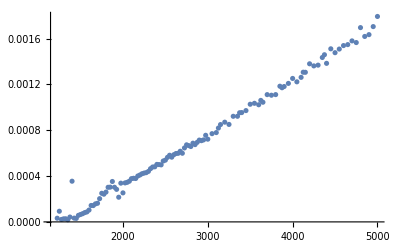

```mathematica
p=250; 
ListPlot[{#1[[2]],#1[[5]]/gxint2[e0bestfit12[p][[1]],12,e0bestfit12[p][[2]],#1[[2]]]}&/@Cases[ddata["fcc",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&tt>1200]]
```

```mathematica
highPplot={100,150,200,250,300,400,500,600,700};
```

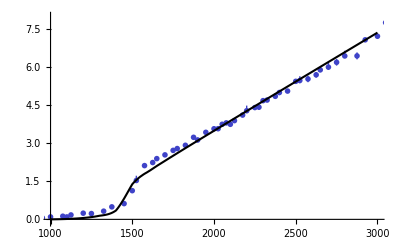
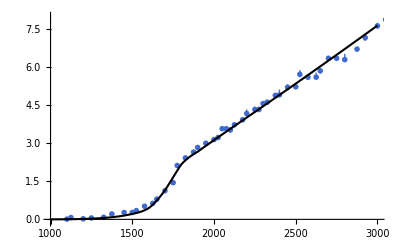
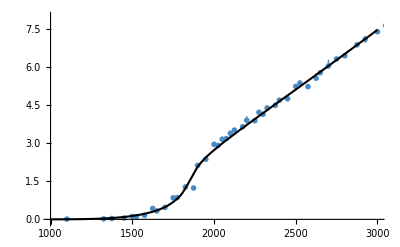
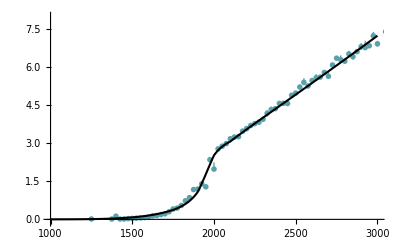
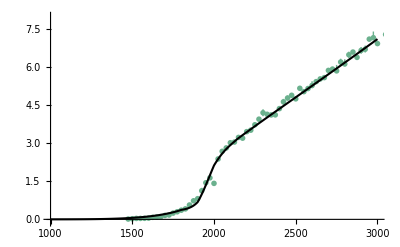
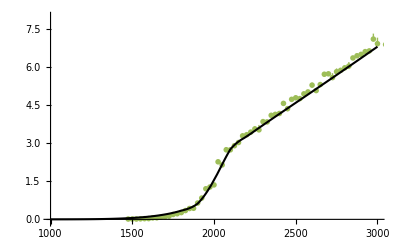
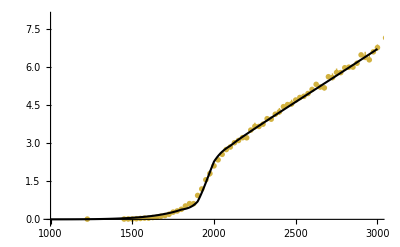
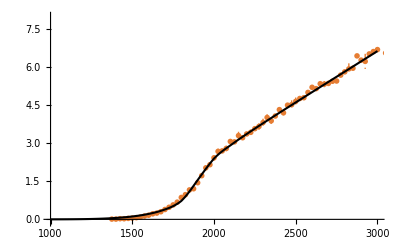

```mathematica
dplots=Table[
Show[{
ErrorListPlot[{{#1[[2]],1*^4*#1[[5]]},ErrorBar[1*^4*#1[[6]]]}&/@Cases[ddata["fcc",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6],
Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.0],ColorData["Rainbow"][p/700.],Dashed],
(*Ticks->{Automatic,{#,ScientificForm@#}&/@Range[0.,5*^-3,1*^-4]},*)
PlotRange->{{1000,3000},{-0.1,8}}],

Plot[1*^4*gxint2[e0bestfit12[p][[1]],12,e0bestfit12[p][[2]],x]*fitest["fcc"][p][x] ,{x,1000,3000},
PlotStyle->Directive[AbsoluteThickness[1.5],Black],
Ticks->{Automatic,{#,ScientificForm@#}&/@Range[0.,5,1]},PlotRange->{All,All}]
}]
,{p,highPplot}]
```

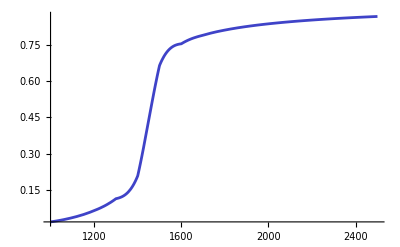
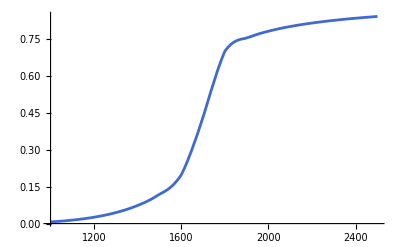
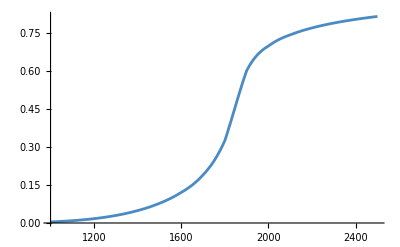
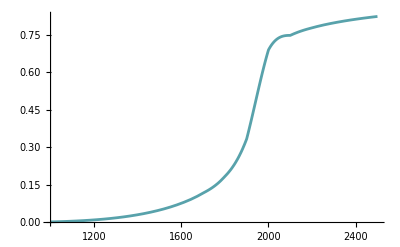
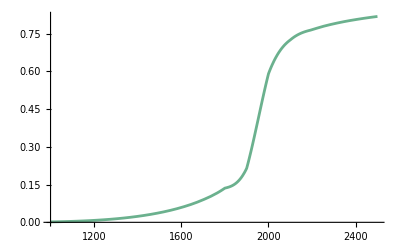
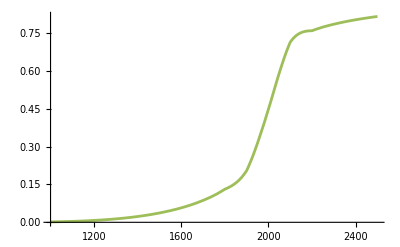
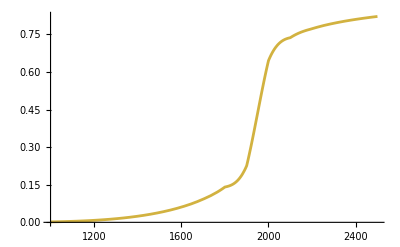
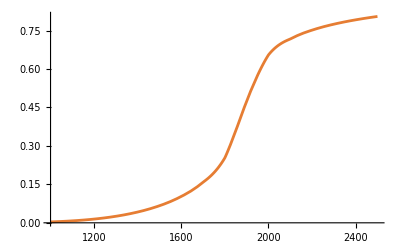

```mathematica
gplots=Table[
Show[{
Plot[gxintfunc[e0bestfit12[p][[1]],12,e0bestfit12[p][[2]],x] ,{x,1000,2500},
PlotStyle->Directive[AbsoluteThickness[2],ColorData["Rainbow"][p/700.]],
Ticks->{Automatic,Automatic},PlotRange->{All,All}]
}]
,{p,highPplot}]
```

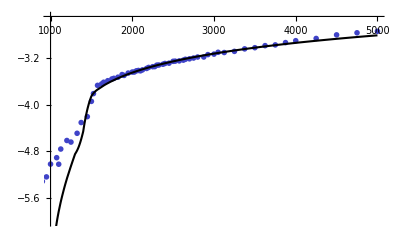
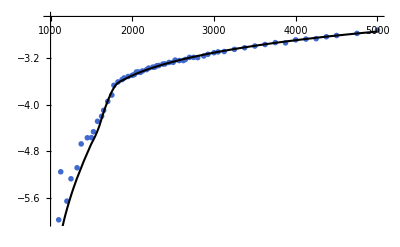
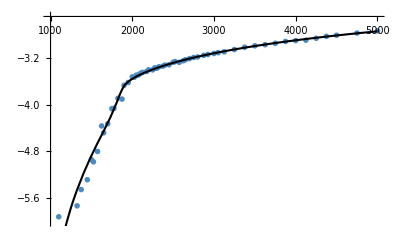
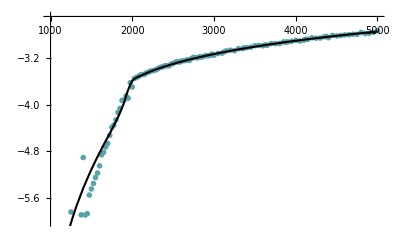
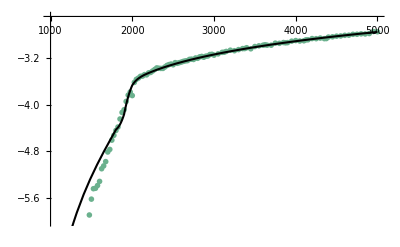
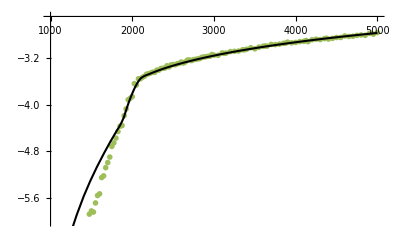
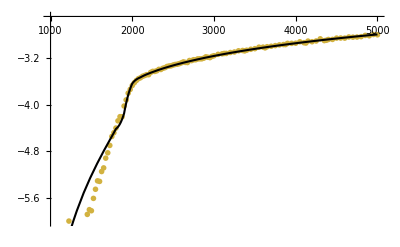
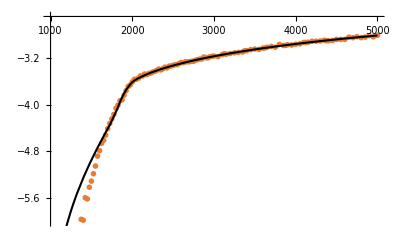

```mathematica
logdplots=Table[
Show[{
ListPlot[{#1[[2]],Log10[#1[[5]]]}&/@Cases[ddata["fcc",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6],
Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.0],ColorData["Rainbow"][p/700.],Dashed],
Ticks->{Automatic,Automatic},PlotRange->{{1000,5000},{-6,-2.5}}],

Plot[Log10[gxint2[e0bestfit12[p][[1]],12,e0bestfit12[p][[2]],x]*fitest["fcc"][p][x]] ,{x,1000,5000},
PlotStyle->Directive[AbsoluteThickness[1.5],Black]
(*Ticks->{Automatic,{#,ScientificForm@#}&/@Range[1.*^-7,1.5*^-3,2*^-5]}*)
,PlotRange->{All,All}]
}]
,{p,highPplot}]
```

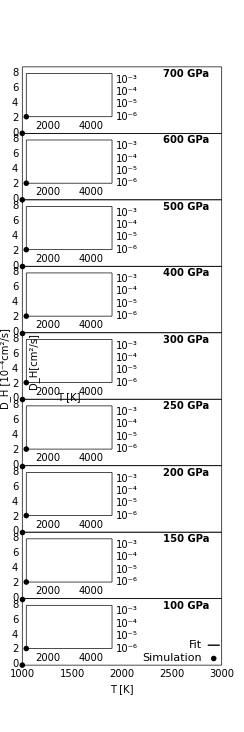

```mathematica
Dplot=Show[{
Graphics[
Table[
FramedInset[logdplots[[i]],Offset[{0.0,0},{0.02,i-0.75}],Offset[{0,0},{0.45,i-0.1}],Intervals->{2,1.5},
LabelOffset->-15,framestyle,
FrameTicks->{LinearTicks,LogarithmTicks,None,None},
TickLabels->{True,True,False,False},
FrameLabel->{If[i==Floor[Length[logdplots]/2]+1,"T [K]",""],If[i==Floor[Length[logdplots]/2]+1,"D_H[cm^2/s]",""]}
],
{i,1,Length[logdplots]}]],
Graphics[
Table[
FramedInset[dplots[[i]],Offset[{0,0},{0,i-1}],Offset[{0,-6},{1,i}],Intervals->{3,1.5},
FrameLabel->{If[i==1,"T [K]",""],If[i==Floor[Length[logdplots]/2]+1,"D_H [10^-4cm^2/s]",""]},
LabelOffset->-5,framestyle,FrameTicks->{If[i==1,LinearTicks,None],None,LinearTicks,LinearTicks}],
{i,1,Length[logdplots]}]],
Graphics[{
Table[
Text[Style[txtFormat[ToString[highPplot[[i]]]<>" GPa"],Bold],Offset[{0.1,-7},{0.82,i}],Offset[{0.0,0},{0.0,0}]],
{i,Range[Length[highPplot]]}],

Inset[plotmark[Black][[1]],Offset[{0.0,0},{0.96,0.1}],{Center,Center}],
{Text["Simulation",Offset[{0.00,0},{0.90,0.1}],{1,0}]},

{Black,AbsoluteThickness[1],Line[{Offset[{0.0,0},{0.99,0.3}],Offset[{0.0,0},{0.93,0.3}]}]},
{Text["Fit",Offset[{0.00,0},{0.90,0.3}],{1,0}]}
}]
}, PlotRange->{{0,1},{0,Length[dplots]}},ImagePadding->{{30,12},{35,5}},ImageSize->onecol,AspectRatio->3]
```

```mathematica
Export[NotebookDirectory[]<>"fit-D.pdf",Dplot,"PDF"]
```

/Users/tc/Dropbox/superionic-water-ice/nnp-simulation-results/nnp-p-r3-1/fit-D.pdf

```mathematica
highPplot={100,200,300,400,500,600,700};
```

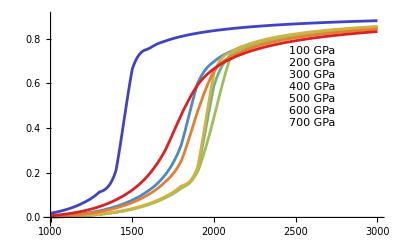

```mathematica
gplots=Show[{
Table[
Plot[gxintfunc[e0bestfit12[p][[1]],12,e0bestfit12[p][[2]],x] ,{x,1000,3000},
PlotStyle->Directive[AbsoluteThickness[2],ColorData["Rainbow"][p/700.]],
Ticks->{Automatic,Automatic},PlotRange->{{1000,3000},{-0.02,0.9}}]
,{p,highPplot}],
Graphics[{
Table[
Text[Style[ToString[highPplot[[i]]]<>" GPa",Fontsize->Small],Offset[{0.1,-12*i},{2600,0.8}],Offset[{0.0,-5},{0,0.0}]],
{i,Range[Length[highPplot]]}],
Table[
{ColorData["Rainbow"][highPplot[[i]]/700.],AbsoluteThickness[1],
Line[{Offset[{10,-12*i},{2600,0.8}],Offset[{30,-12*i},{2600,0.8}]}]},
{i,Range[Length[highPplot]]}]
}]
}]
```

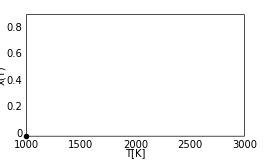

```mathematica
gplot=Show[
FramedGraphics[gplots,
FrameLabel->{"T[K]","x(T)"},Intervals->3,LabelOffset->-12,framestyle],
PlotRange->All,ImageSize->onecol*1.1,AspectRatio->0.6,ImagePadding->{{30,10},{20,10}}
]
```

```mathematica
Export[NotebookDirectory[]<>"fit-gx.pdf",gplot,"PDF"]
```

/Users/tc/Dropbox/superionic-water-ice/nnp-simulation-results/nnp-p-r3-1/fit-gx.pdf

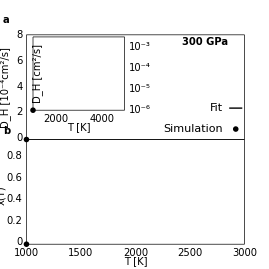

```mathematica
p=300;
mainDplot=Show[{
Graphics[{
FramedInset[logdplots[[5]],Offset[{0.0,0},{0.03,2-0.72}],Offset[{0,0},{0.45,2-0.02}],Intervals->{2,1.5},
LabelOffset->-12,framestyle,
FrameTicks->{LinearTicks,LogarithmTicks,None,None},
TickLabels->{True,True,False,False},
FrameLabel->{"T [K]","D_H [cm^2/s]"}],
FramedInset[dplots[[5]],Offset[{0,0},{0,1}],Offset[{0,0},{1,2}],Intervals->{3,1.5},
FrameLabel->{"","D_H [10^-4cm^2/s]"},
LabelOffset->-1,framestyle,
FrameTicks->{LinearTicks,None,None,LinearTicks},
TickLabels->{False,False,False,True}],

FramedInset[gplots,Offset[{0,0},{0,0}],Offset[{0,-6},{1,1}],Intervals->{3,1.5},
FrameLabel->{"T [K]","x(T)"},
LabelOffset->-12,framestyle,
FrameTicks->{LinearTicks,None,None,LinearTicks}]
}],
Graphics[{
Text[Style[txtFormat["a"],Bold,Large],Offset[{-20,15},{0,2}],Offset[{0.0,0},{0.0,0}]],
Text[Style[txtFormat["b"],Bold,Large],Offset[{-20,15-6},{0,1}],Offset[{0.0,0},{0.0,0}]],
Text[Style[txtFormat["300 GPa"],Bold],Offset[{0.1,-7},{0.82,2}],Offset[{0.0,0},{0.0,0}]],

Inset[plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],Offset[{0.0,0},{0.96,1.1}],{Center,Center}],
{Text["Simulation",Offset[{0.00,0},{0.90,1.1}],{1,0}]},

{Black,AbsoluteThickness[1],Line[{Offset[{0.0,0},{0.99,1.3}],Offset[{0.0,0},{0.93,1.3}]}]},
{Text["Fit",Offset[{0.00,0},{0.90,1.3}],{1,0}]}
}]
}, PlotRange->{{0,1},{0,2}},ImagePadding->{{35,12},{25,5}},ImageSize->onecol*1.1,AspectRatio->1.]
```

```mathematica
Export[NotebookDirectory[]<>"main-fit-D.pdf",mainDplot,"PDF"]
```

/Users/tc/Dropbox/superionic-water-ice/nnp-simulation-results/nnp-p-r3-1/main-fit-D.pdf

```mathematica
Show[{
Table[
ErrorListPlot[{{#1[[2]],#1[[5]]},ErrorBar[#1[[6]]]}&/@Cases[ddata["fcc",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6],
Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.5],ColorData["Rainbow"][p/800.],Dashed],PlotRange->{All,All}]
,{p,{250,400,500,700}}],
Table[
Plot[gxint2[e0bestfit[p][[1]],12,e0bestfit12[p][[2]],x]*fitest["fcc"][p][x] ,{x,1000,5000},
PlotStyle->Directive[AbsoluteThickness[1.5],ColorData["Rainbow"][p/700.]],PlotRange->{All,All}]
,{p,{250,400,500,700}}]
}, PlotRange->{{1000,3500},{0,0.001}}]
```

$Aborted

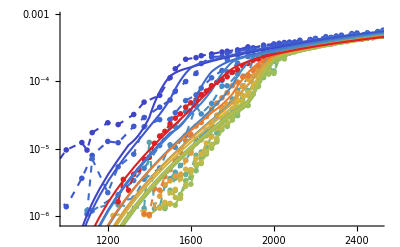

```mathematica
Show[{
Table[
ListLogPlot[{#1[[2]],#1[[5]]}&/@Cases[ddata["fcc",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6],
Joined->True,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/800.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.5],ColorData["Rainbow"][p/700.],Dashed],PlotRange->{All,All}]
,{p,highP}],
Table[
LogPlot[gxint2[e0bestfit12[p][[1]],12,e0bestfit12[p][[2]],x]*fitest["fcc"][p][x] ,{x,1000,3000},
PlotStyle->Directive[AbsoluteThickness[1.5],ColorData["Rainbow"][p/700.]],PlotRange->{All,All}]
,{p,highP}]
}, PlotRange->{{1000,2500},{-14,-7}}]
```

## fits for Pbcm

```mathematica
highPplot={250,300,400,500,600,700};
```

```mathematica
Clear[fitdatanow]
```

```mathematica
Table[
fitdatanow[pnow]={#1[[2]],Re[#1[[5]]/fitest["Pbcm"][pnow][#1[[2]]]]}&/@Cases[ddata["Pbcm",pnow],{pp_,tt_,do_,_,dh_,_}/;tt>1000 &&tt< 3000];
int=Interpolation[ Flatten[Table[{{e0,cr0},loss[e0,12,cr0,fitdatanow[pnow]]},
{e0,6500,9000,125},{cr0,0.7,1.1,0.0125}],1]];
bestfit=NMinimize[{int[x,y],0.7<y<1.1,6500<x<9000},{x,y}];
pbcme0bestfit12[pnow]={x,y}/.bestfit[[2]];
errors=#1[[6]]&/@Cases[ddata["Pbcm",pnow],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&tt>1500];
fitest["Pbcm"][pnow]=NonlinearModelFit[
{#1[[2]],Re[#1[[5]]/gxint2[pbcme0bestfit12[pnow][[1]],12,pbcme0bestfit12[pnow][[2]],#1[[2]]]]}&/@Cases[ddata["Pbcm",pnow],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&tt>1000],
empiricalD[{estD0,estgamma,1000},x],
{{estD0,0.},{estgamma,1},{estT0,1000}},
x,MaxIterations->10000];
{pnow,bestfit}
,{pnow,highPplot},{loop,1,4}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{{250,{0.19427,{x→8942.32,y→1.03721}}},{250,{0.308684,{x→8949.66,y→1.0375}}},{250,{0.306661,{x→8949.66,y→1.0375}}},{250,{0.306661,{x→8949.66,y→1.0375}}}},{{300,{1.03369,{x→8943.5,y→1.03748}}},{300,{0.373746,{x→8944.,y→1.03702}}},{300,{0.371998,{x→8944.,y→1.03702}}},{300,{0.371991,{x→8944.,y→1.03702}}}},{{400,{0.361197,{x→9000.,y→1.05747}}},{400,{0.344864,{x→9000.,y→1.05745}}},{400,{0.344829,{x→9000.,y→1.05745}}},{400,{0.344829,{x→9000.,y→1.05745}}}},{{500,{0.16123,{x→8944.71,y→1.0375}}},{500,{0.117188,{x→8935.57,y→1.0375}}},{500,{0.121595,{x→8935.37,y→1.0375}}},{500,{0.121693,{x→8935.37,y→1.0375}}}},{{600,{-0.222849,{x→8942.18,y→1.1}}},{600,{-0.22249,{x→8942.3,y→1.1}}},{600,{-0.222482,{x→8942.3,y→1.1}}},{600,{-0.222482,{x→8942.3,y→1.1}}}},{{700,{0.0483895,{x→7920.27,y→1.03167}}},{700,{0.0391442,{x→7918.97,y→1.03191}}},{700,{0.0392811,{x→7918.95,y→1.03192}}},{700,{0.0392841,{x→7918.95,y→1.03192}}}}}

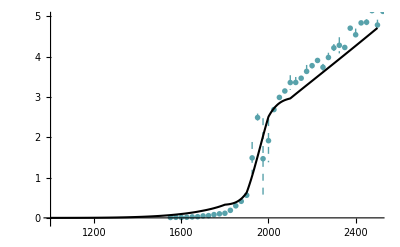
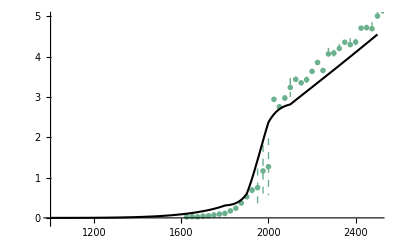
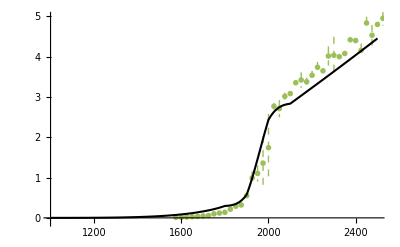
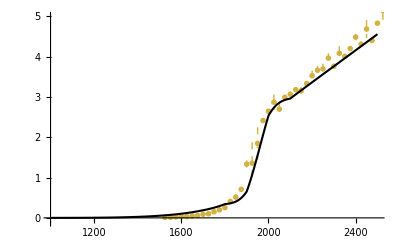
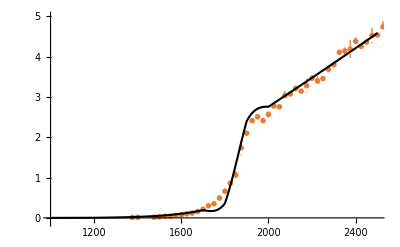
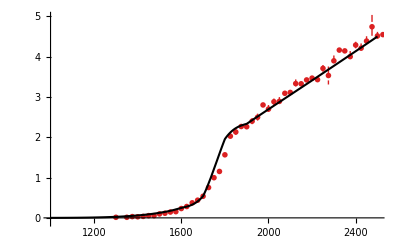

```mathematica
pbcmdplots=Table[
Show[{
ErrorListPlot[{{#1[[2]],1*^4*#1[[5]]},ErrorBar[1*^4*#1[[6]]]}&/@Cases[ddata["Pbcm",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6],
Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.0],ColorData["Rainbow"][p/700.],Dashed],
(*Ticks->{Automatic,{#,ScientificForm@#}&/@Range[0.,5*^-3,1*^-4]},*)
PlotRange->{{1000,2500},{-0.1,5}}],

Plot[1*^4*gxint2[pbcme0bestfit12[p][[1]],12,pbcme0bestfit12[p][[2]],x]*fitest["Pbcm"][p][x] ,{x,1000,2500},
PlotStyle->Directive[AbsoluteThickness[1.5],Black],
Ticks->{Automatic,{#,ScientificForm@#}&/@Range[0.,5,1]},PlotRange->{All,All}]
}]
,{p,highPplot}]
```

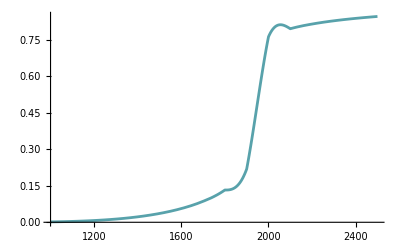
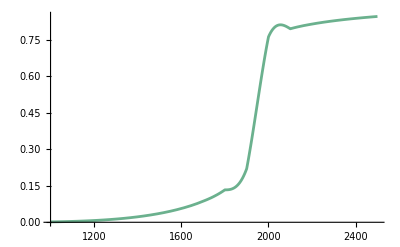
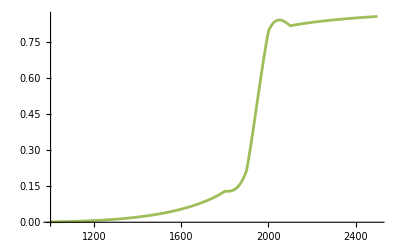
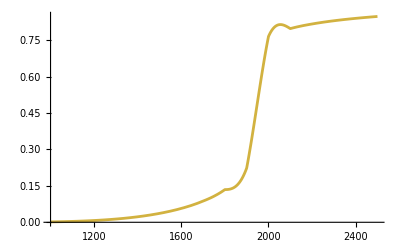
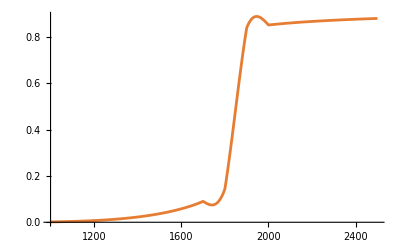
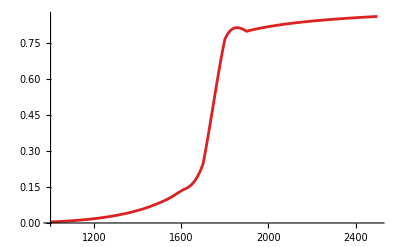

```mathematica
pbcmgplots=Table[
Show[{
Plot[gxintfunc[pbcme0bestfit12[p][[1]],12,pbcme0bestfit12[p][[2]],x] ,{x,1000,2500},
PlotStyle->Directive[AbsoluteThickness[2],ColorData["Rainbow"][p/700.]],
Ticks->{Automatic,Automatic},PlotRange->{All,All}]
}]
,{p,highPplot}]
```

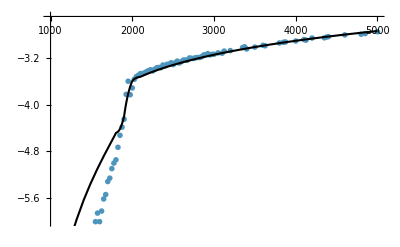
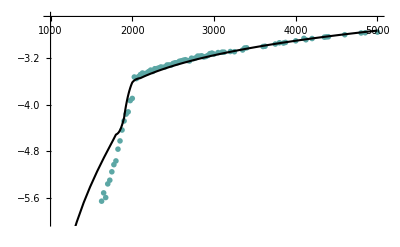
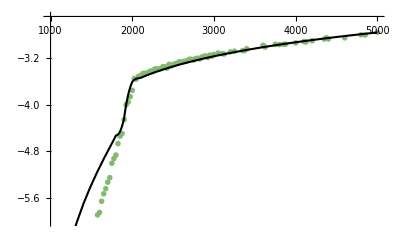
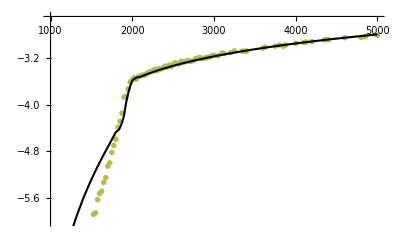
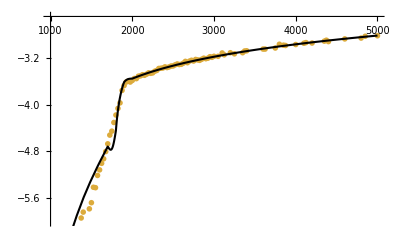
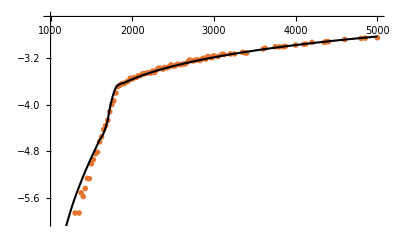

```mathematica
pbcmlogdplots=Table[
Show[{
ListPlot[{#1[[2]],Log10[#1[[5]]]}&/@Cases[ddata["Pbcm",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6],
Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/700.],ColorData["Rainbow"][p/700.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.0],ColorData["Rainbow"][p/800.],Dashed],
Ticks->{Automatic,Automatic},PlotRange->{{1000,5000},{-6,-2.5}}],

Plot[Log10[gxint2[pbcme0bestfit12[p][[1]],12,pbcme0bestfit12[p][[2]],x]*fitest["Pbcm"][p][x]] ,{x,1000,5000},
PlotStyle->Directive[AbsoluteThickness[1.5],Black]
(*Ticks->{Automatic,{#,ScientificForm@#}&/@Range[1.*^-7,1.5*^-3,2*^-5]}*)
,PlotRange->{All,All}]
}]
,{p,highPplot}]
```

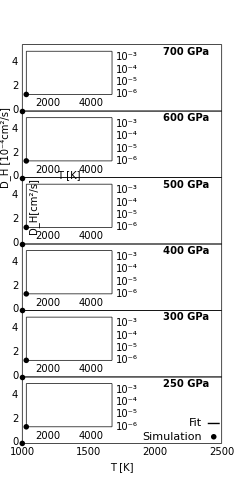

```mathematica
pbcmDplot=Show[{
Graphics[
Table[
FramedInset[pbcmlogdplots[[i]],Offset[{0.0,0},{0.02,i-0.75}],Offset[{0,0},{0.45,i-0.1}],Intervals->{2,1.5},
LabelOffset->-15,framestyle,
FrameTicks->{LinearTicks,LogarithmTicks,None,None},
TickLabels->{True,True,False,False},
FrameLabel->{If[i==Floor[Length[logdplots]/2]+1,"T [K]",""],If[i==Floor[Length[pbcmlogdplots]/2]+1,"D_H[cm^2/s]",""]}
],
{i,1,Length[pbcmlogdplots]}]],
Graphics[
Table[
FramedInset[pbcmdplots[[i]],Offset[{0,0},{0,i-1}],Offset[{0,-6},{1,i}],Intervals->{3,1.5},
FrameLabel->{If[i==1,"T [K]",""],If[i==Floor[Length[logdplots]/2]+1,"D_H [10^-4cm^2/s]",""]},
LabelOffset->-5,framestyle,FrameTicks->{If[i==1,LinearTicks,None],None,LinearTicks,LinearTicks}],
{i,1,Length[pbcmlogdplots]}]],
Graphics[{
Table[
Text[Style[txtFormat[ToString[highPplot[[i]]]<>" GPa"],Bold],Offset[{0.1,-7},{0.82,i}],Offset[{0.0,0},{0.0,0}]],
{i,Range[Length[highPplot]]}],
Inset[plotmark[Black][[1]],Offset[{0.0,0},{0.96,0.1}],{Center,Center}],
{Text["Simulation",Offset[{0.00,0},{0.90,0.1}],{1,0}]},
{Black,AbsoluteThickness[1],Line[{Offset[{0.0,0},{0.99,0.3}],Offset[{0.0,0},{0.93,0.3}]}]},
{Text["Fit",Offset[{0.00,0},{0.90,0.3}],{1,0}]}
}]
}, PlotRange->{{0,1},{0,Length[pbcmdplots]}},ImagePadding->{{30,12},{35,5}},ImageSize->onecol,AspectRatio->2]
```

```mathematica
Export[NotebookDirectory[]<>"pbcm-fit-D.pdf",pbcmDplot,"PDF"]
```

/Users/tc/Dropbox/superionic-water-ice/nnp-simulation-results/nnp-p-r3-1/pbcm-fit-D.pdf

## fits for bcc

```mathematica
lowP[[2;;]]
```

{30,50,75,100,125,150,175,200,250}

```mathematica
Clear[fitdatanow]
```

```mathematica
Table[
fitdatanow[pnow]={#1[[2]],Re[#1[[5]]/fitest["bcc"][pnow][#1[[2]]]]}&/@Cases[ddata["bcc",pnow],{pp_,tt_,do_,_,dh_,_}/;tt>1000 &&tt< 3500&&do<1*^-4];
int=Interpolation[ Flatten[Table[{{e0,cr0},loss[e0,100,cr0,fitdatanow[pnow]]},
{e0,3000,20000,250},{cr0,0.7,1.2,0.0125}],1]];
bestfit=NMinimize[{int[x,y],0.7<y<1.2,3000<x<20000},{x,y}];
bcce0bestfit100[pnow]={x,y}/.bestfit[[2]];
errors=#1[[6]]&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&tt>2000];
fitest["bcc"][pnow]=NonlinearModelFit[
{#1[[2]],Re[#1[[5]]/gxint2[bcce0bestfit100[pnow][[1]],100,bcce0bestfit100[pnow][[2]],#1[[2]]]]}&/@Cases[ddata["bcc",pnow],{pp_,tt_,do_,_,dh_,_}/;do<1*^-4 &&tt>2000],
empiricalD[{estD0,estgamma,1000},x],
{{estD0,0.},{estgamma,1},{estT0,1000}},
x,MaxIterations->10000];
{pnow,bestfit}
,{pnow,lowP[[2;;]]},{loop,1,2}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {y} = {0.}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

{{{30,{13.9783,{x→6909.13,y→1.14316}}},{30,{14.0364,{x→6891.86,y→1.2}}}},{{50,{7.94533,{x→10069.7,y→1.15764}}},{50,{8.43833,{x→10699.4,y→1.19441}}}},{{75,{0.179016,{x→12779.,y→1.02117}}},{75,{0.180187,{x→12778.9,y→1.02117}}}},{{100,{3.75621,{x→14344.8,y→1.04434}}},{100,{5.22586,{x→14582.9,y→1.08208}}}},{{125,{2.02932,{x→15621.9,y→1.0125}}},{125,{2.3002,{x→15895.6,y→1.051}}}},{{150,{-0.0245552,{x→16625.6,y→1.0625}}},{150,{-0.0378457,{x→16625.1,y→1.0622}}}},{{175,{0.0877678,{x→17032.5,y→1.05871}}},{175,{0.0637113,{x→17037.5,y→1.05851}}}},{{200,{-0.00188219,{x→18124.9,y→1.1625}}},{200,{0.0159809,{x→17169.6,y→1.01723}}}},{{250,{-0.0140858,{x→18413.4,y→1.18059}}},{250,{0.12554,{x→16932.,y→0.991329}}}}}

Table[
 fitdatanow[pnow] = {#1[[2]], Re[#1[[5]]/fitest["bcc"][pnow][#1[[2]]]]} & /@ Cases[ddata["bcc", pnow], {pp_, tt_, do_, _, dh_, _} /; tt > 1000 && tt < 3500 && do < 1*^-4];
 int = Interpolation[ Flatten[Table[{{e0, cr0}, loss[e0, 50, cr0, fitdatanow[pnow]]},
     {e0, 1000, 17000, 250}, {cr0, 0.8, 1.12, 0.0125}], 1]];
 bestfit = NMinimize[{int[x, y], 0.8 < y < 1.0, 1000 < x < 17000}, {x, y}];
 bcce0bestfit50[pnow] = {x, y} /. bestfit[[2]];
 errors = #1[[6]] & /@ Cases[ddata["bcc", p], {pp_, tt_, do_, _, dh_, _} /; do < 1*^-4 && tt > 2000];
 fitest["bcc"][p] = NonlinearModelFit[
   {#1[[2]], Re[#1[[5]]/gxint2[bcce0bestfit50[p][[1]], 50, bcce0bestfit50[p][[2]], #1[[2]]]]} & /@ Cases[ddata["bcc", p], {pp_, tt_, do_, _, dh_, _} /; do < 1*^-4 && tt > 2000],
   empiricalD[{estD0, estgamma, 800}, x],
   {{estD0, 0.}, {estgamma, 1}, {estT0, 1000}},
   x, MaxIterations -> 10000];
 {pnow, bestfit}
 , {pnow, lowP[[2 ;;]]}, {loop, 1, 2}]

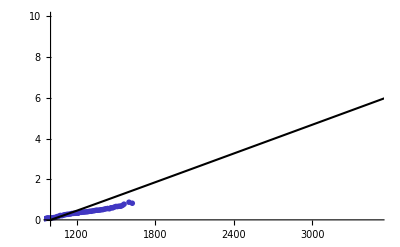
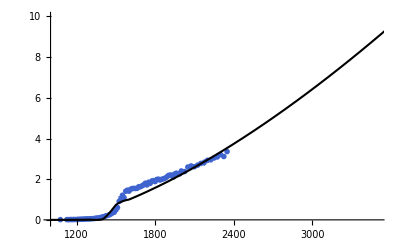
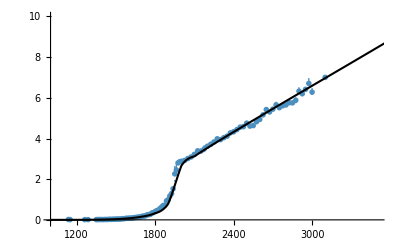
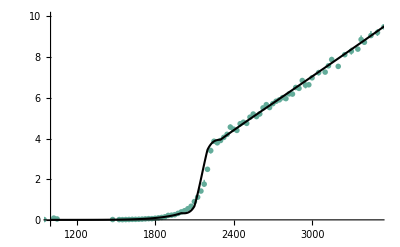
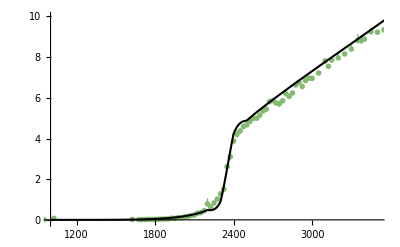
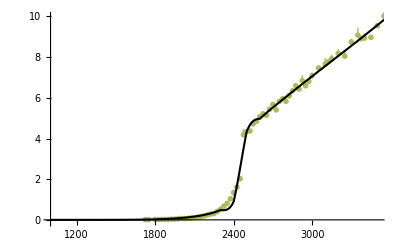
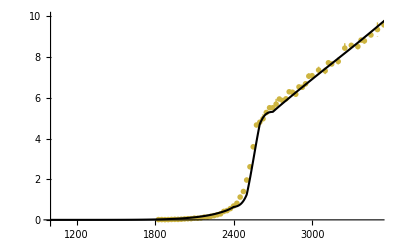
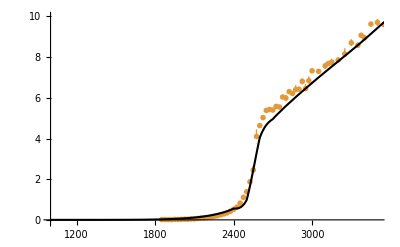

```mathematica
bccdplots=Table[
Show[{
ErrorListPlot[{{#1[[2]],1*^4*#1[[5]]},ErrorBar[1*^4*#1[[6]]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6&&do<1*^-5],
Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/250.],ColorData["Rainbow"][p/250.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.0],ColorData["Rainbow"][p/250.],Dashed],
PlotRange->{{1000,3500},{-0.1,10}}],

Plot[1*^4*gxint2[bcce0bestfit100[p][[1]],100,bcce0bestfit100[p][[2]],x]*fitest["bcc"][p][x] ,{x,1000,5000},
PlotStyle->Directive[AbsoluteThickness[1.5],Black],PlotRange->{All,All}]
}]
,{p,lowP[[2;;]]}]
```

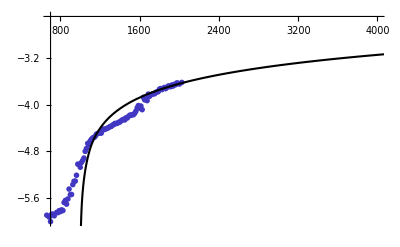
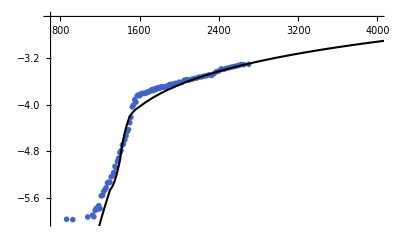
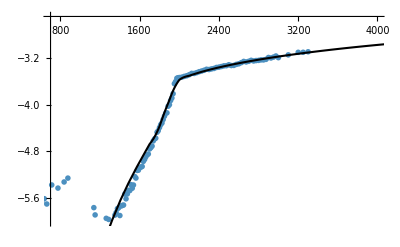
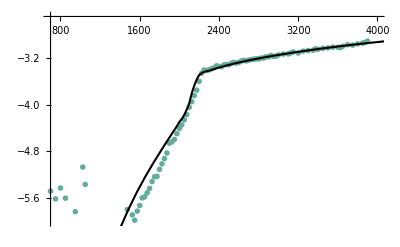
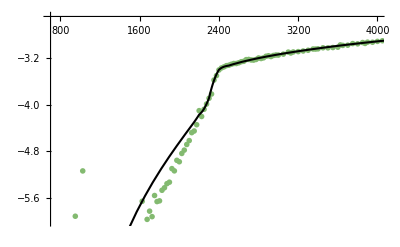
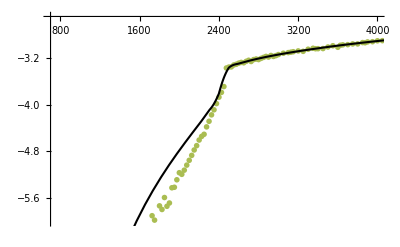
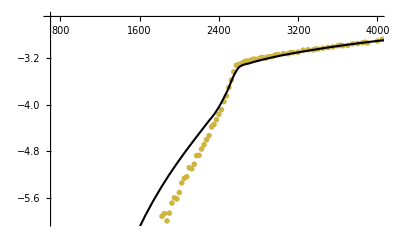
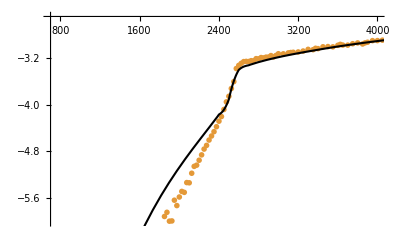

```mathematica
bcclogdplots=Table[
Show[{
ListPlot[{#1[[2]],Log10[#1[[5]]]}&/@Cases[ddata["bcc",p],{pp_,tt_,do_,_,dh_,_}/;dh>1*^-6&&do<1*^-4],
Joined->False,PlotMarkers->plotmark[ColorData["Rainbow"][p/250.],ColorData["Rainbow"][p/250.]][[1]],
PlotStyle->Directive[AbsoluteThickness[1.0],ColorData["Rainbow"][p/250.],Dashed],
Ticks->{Automatic,Automatic},PlotRange->{{700,4000},{-6,-2.5}}],

Plot[Log10[gxint2[bcce0bestfit50[p][[1]],50,bcce0bestfit50[p][[2]],x]*fitest["bcc"][p][x] ],{x,1000,5000},
PlotStyle->Directive[AbsoluteThickness[1.5],Black],
Ticks->{Automatic,Automatic},PlotRange->{All,All}]
}]
,{p,lowP[[2;;]]}]
```

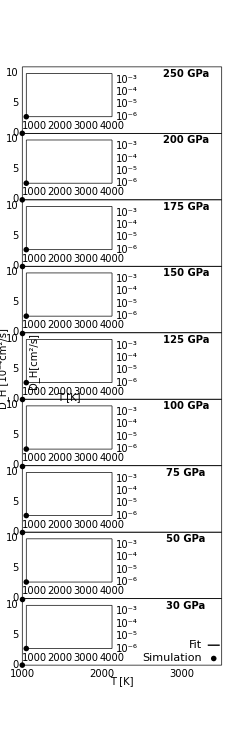

```mathematica
bccDplot=Show[{
Graphics[
Table[
FramedInset[bcclogdplots[[i]],Offset[{0.0,0},{0.02,i-0.75}],Offset[{0,0},{0.45,i-0.1}],Intervals->{2,1.5},
LabelOffset->-15,framestyle,
FrameTicks->{LinearTicks,LogarithmTicks,None,None},
TickLabels->{True,True,False,False},
FrameLabel->{If[i==Floor[Length[logdplots]/2]+1,"T [K]",""],If[i==Floor[Length[logdplots]/2]+1,"D_H[cm^2/s]",""]}
],
{i,1,Length[bcclogdplots]}]],
Graphics[
Table[
FramedInset[bccdplots[[i]],Offset[{0,0},{0,i-1}],Offset[{0,-6},{1,i}],Intervals->{2,1.5},
FrameLabel->{If[i==1,"T [K]",""],If[i==Floor[Length[logdplots]/2]+1,"D_H [10^-4cm^2/s]",""]},
LabelOffset->-13,framestyle,FrameTicks->{If[i==1,LinearTicks,None],None,LinearTicks,LinearTicks}],
{i,1,Length[bcclogdplots]}]],
Graphics[{
Table[
Text[Style[txtFormat[ToString[lowP[[2;;]][[i]]]<>" GPa"],Bold],Offset[{0.1,-7},{0.82,i}],Offset[{0.0,0},{0.0,0}]],
{i,Range[Length[lowP[[2;;]]]]}],
Inset[plotmark[Black][[1]],Offset[{0.0,0},{0.96,0.1}],{Center,Center}],
{Text["Simulation",Offset[{0.00,0},{0.90,0.1}],{1,0}]},
{Black,AbsoluteThickness[1],Line[{Offset[{0.0,0},{0.99,0.3}],Offset[{0.0,0},{0.93,0.3}]}]},
{Text["Fit",Offset[{0.00,0},{0.90,0.3}],{1,0}]}
}]
}, PlotRange->{{0,1},{0,Length[bccdplots]}},ImagePadding->{{30,12},{35,5}},ImageSize->onecol,AspectRatio->3]
```

```mathematica
Export[NotebookDirectory[]<>"bcc-fit-D.pdf",bccDplot,"PDF"]
```

/Users/tc/Dropbox/superionic-water-ice/nnp-simulation-results/nnp-p-r3-1/bcc-fit-D.pdf

## Save things

```mathematica
Save[NotebookDirectory[]<>"11Aug-savedgxint.m",gxint];
```